```mathematica
(* ΑΣΚΗΣΗ 1 *)
(* Ερώτημα α *)
```

```mathematica
Integrate[γ*π^(-1)/(γ^2+t^2),{t, -Infinity, x}]
```

ConditionalExpression[(γ (1/2 π √(1/γ^2)+ArcTan[x/γ]/γ))/π, ]

```mathematica
F(x)=1/π*arctan(x/γ)+1/2
```

Set::write: Tag Times in F x is Protected.

1/2+(arctan x)/(π γ)

```mathematica
Solve[y == (1/π)*ArcTan[x/γ]+1/2, x]
```

{{x→ConditionalExpression[γ Tan[1/2 π (-1+2 y)], ]}}

```mathematica
γ=0.1;n=100000;rn=Table[0,{n}];
```

```mathematica
Do[x=γ*Tan[Pi*(Random[]-1/2)];
rn[[i]]=x;,{i,1,n}];
```

```mathematica
pl1=Histogram[rn,{Table[j,{j,-1.5,1.5,0.01}]},"ProbabilityDensity", ChartStyle -> Blue];
```

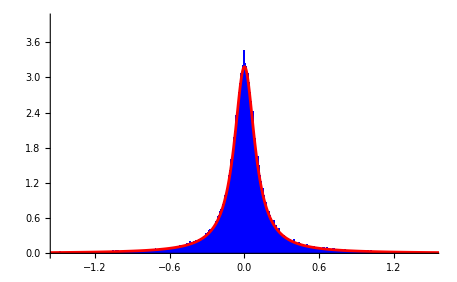

```mathematica
pl2=Plot[γ/(Pi (γ^2+x^2)), {x,-5,5}, PlotStyle->Red, PlotRange->{0,4}];
Show[pl1,pl2, PlotRange->{{-1.5,1.5}, {0,4}}]
```

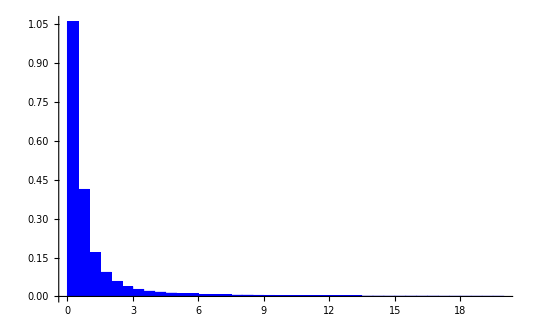

```mathematica
(* Ερώτημα β *)
γ=0.1;k=100000;rn=Table[0,{k}];n=10;
Do[x=Max[Table[γ*Tan[Pi*(RandomReal[]-1/2)],{n}]];
rn[[i]]=x;,{i,1,k}];
pl1=Histogram[rn,{Table[j,{j,0,20,0.5}]},"ProbabilityDensity", ChartStyle -> Blue]
```

```mathematica
(* Ερώτημα γ *)

γ=0.1; k=10000;rn=Table[0,{k}];a={};
Do[
Do[x=Max[Table[γ*Tan[Pi*(RandomReal[]-1/2)],{n}]];
rn[[i]]=Min[x,10]; ,{i,1,k}];
Print[{n,Mean[rn]}];
AppendTo[a,{n,Mean[rn]}];
,{n,1,30}]
ListPlot[a]
```

{1,-0.237589}

{2,0.30455}

{3,0.453718}

{4,0.594148}

{5,0.705464}

{6,0.836155}

{7,0.942131}

{8,1.03848}

{9,1.12945}

{10,1.20809}

{11,1.35076}

{12,1.40943}

{13,1.50934}

{14,1.61211}

{15,1.6627}

{16,1.76697}

{17,1.86411}

{18,1.96214}

{19,1.98593}

{20,2.02008}

{21,2.16214}

{22,2.22094}

{23,2.23517}

{24,2.39261}

{25,2.33561}

{26,2.48482}

{27,2.50586}

{28,2.57069}

{29,2.61904}

{30,2.72262}

-Graphics-

```mathematica
(* Ερώτημα δ *)

k=10000;rn=Table[0,{k}];a={};
Do[
Do[x=Max[Table[RandomReal[NormalDistribution[0,0.5]],{n}]];
rn[[i]]=x; ,{i,1,k}];
Print[{n,Mean[rn]}];
AppendTo[a, {n,Mean[rn]}];
,{n,1,30}]
ListPlot[a]
```

{1,-0.00080168}

{2,0.284906}

{3,0.423812}

{4,0.512186}

{5,0.578509}

{6,0.632008}

{7,0.67632}

{8,0.712195}

{9,0.741796}

{10,0.770089}

{11,0.789483}

{12,0.819184}

{13,0.834312}

{14,0.854068}

{15,0.868091}

{16,0.889365}

{17,0.894272}

{18,0.910801}

{19,0.920764}

{20,0.933382}

{21,0.945994}

{22,0.955695}

{23,0.963098}

{24,0.978766}

{25,0.984718}

{26,0.993075}

{27,0.997394}

{28,1.00995}

{29,1.01461}

{30,1.02615}

-Graphics-

Histogram::hbins: The bin specification PDF cannot be used to determine either how many or which bins to use.

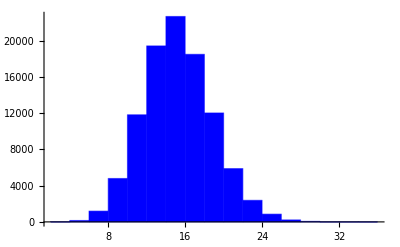

15.2579

```mathematica
(* ΑΣΚΗΣΗ 2 *)

(* Ερώτημα α *)

a=2; b=4; n=100000; r1=Table[0,{n}];λ=20;
Do[U=Random[];
p=Exp[-λ];F=p;i=0;
While[U>F,p=p*λ/(i+1);F=F+p; i=i+1];
N0=i;
W=Sum[(-Log[1-Random[]]/a)^(1/b),{N0}];
r1[[j]]=W;
,{j,1,n}];

Histogram[r1,"PDF", ChartStyle->Blue]
Mean[r1]
```

```mathematica
(* Ερώτημα β *)
SRL = Sort[r1];
A=SRL[[0.95*n]]
```

21.3142

```mathematica
(* Ερώτημα γ *)
a=2;b=4;n=10000;λ=20;m=0;h=0;
Do[U=Random[];
p=Exp[-λ];F=p;i=0;
While[U>F,p=p*λ/(i+1);F=F+p;i=i+1];
N0=i;
W=Sum[(-Log[1-Random[]]/a)^(1/b),{N0}];
If[W>A, m=m+W-A;h++];
,{j,1,n}];
N[m/h]
```

1.65935

```mathematica
(* ΑΣΚΗΣΗ 3 *)
(* Ερώτημα α *)
x={1,2,3,4};p={0.4,0.3,0.2,0.1};n=1000;
M=Table[0,{n}];
Do[
A={0,0,0,0};j=0;
While[Sum[A[[i]],{i,1,4}]<4,
U=RandomReal[];i=1;cp=p[[1]];
A[[x[[i]]]]=1;j++
];
M[[k]]=j;
,{k,1,n}]
Mean[N[M]]
Histogram[M, PlotStyle->Blue]
```

```mathematica
(* Ερώτημα β *)
j=0; Do[If[M[[i]]≥15,j++],{i,1,n}]
Print[N[j/n]]

(*Ερώτημα γ *)
x={1,2,3,4};p={0.4,0.3,0.2,0.1};n=100000;
L=Table[0,{n}];
Do[
A={0,0,0,0};j=0;
While[Sum[A[[i]],{i,1,4,}]<4,
U=RandomReal[];i=1;cp=p[[1]];
While[U>cp,i=i+1;cp=cp+p[[i]]];
A[[x[[i]]]]=1;j++
];
L[[k]]=x[[i]];
,{k,1,n}]
LL=Sort[Tally[L]]
Table[{LL[[i,1]],N[LL[[i,2]]/n]},{i,1,4}]
```